## Constants

```mathematica
Needs["NumericalCalculus`"]
(*Constants*)h=6.62606896*^-34;               (*Planck constant (J.s)*)
hbar=h/(2*Pi);
Kb=1.380649*^-23;               (*Boltzmann constant*)
au=1.6605*^-27;
mass=4.0026*au;                 (*He4 mass*)
Temp=0.25;                       (*Temperature in Kelvin*)
NValue=10000;                     (*Set the value of N*)
L1 = 1000*^-9;                 (*Set the value of Longitudal Length*)
Lt= 100*^-9;          (*Set the value of Transverse Length same as the eigenvalue dataset*)
(*Read data from the text file with a space in the folder name*)
eigenvalues=Import["/Users/Cem/Desktop/Bose-einstein_Condensation/ShapeEffects/eigList.csv","CSV"];

thetascale =45/(Length[eigenvalues]-1);
```

## Functions

```mathematica
lambda[T_]:=h/(√(2 Pi mass Kb T))(*De Broglie wavelength*)

(*Classical particle density of chore shell structre*) 
density[Lt_,pn_] := pn/(Lt^2(1-0.7^2))

qdensity[T_]:=1/(lambda[T])^2 (*quantum density*)

dimlessdensity[T_,Lt_,pn_]:=density[Lt,pn]/qdensity[T]  (*dimensionless density*)


ε0= ((eigenvalues[[46]][[1]])/Lt)^2 hbar^2/(2 mass);    (*ground state energy of our system, where rotation is 45 degree since minimum energy is when the inner shell rotatiioin is 45 degree*)

T0 = ε0/Kb; (*Ground state dimensionless temperature for normalization of dimensionlesss temperature*)
dimlessε0[T_] :=ε0/(Kb T)   (*dimensionless reference energy *)

dimlessε[eig_,T_,L_]:= (eig/L)^2 hbar^2/(2 mass)1/(Kb T);    

calcN[T_,Lt_, nr_] := pn/.FindRoot[  dimlessdensity[T,Lt,pn]/dimlessε0[T]==nr,{pn,1, 0, 1000000}]  (* using dimensionless reference density nr, calculating N particle number needed*)
calcT[dimlessT_]:= dimlessT T0

Lc[T_]:=h/(2 √(2 mass Kb T))      (*Confinement Length*) 

Leff[Lt_] := h/(2 √(2mass ε0))


BoseFac[eig_,T_,L_,Λ_]:=1/(Exp[dimlessε[eig,T,L]-Λ]-1)   (*Bose Distribution*)


(*************************************************************************************************************************)
(************************************************SUMMATION FUNCTIONS********************************************************)
(*************************************************************************************************************************)
Summucalc[eig_,T_,L_,pn_]:=lam/.FindRoot[SumNBE[eig,T,L,lam ]==pn,{lam,dimlessε[Min[eig],T,L] -Log[1/pn + 1],-100,  dimlessε[Min[eig],T,L]}](*Calculating dimensionless Chemical Potential*)

SumNBE[eig_,T_,L_,Λ_]:=Total[BoseFac[eig,T,L,Λ]](*Calculating N particle Number*)


SumN0BE[eig_,T_,L_,Λ_]:=Total[1/(Exp[dimlessε[eig[[1;;4]],T,L]-Λ]-1)]/Total[BoseFac[eig,T,L,Λ]](*Calculating Condensation Fraction*)


SumUBE[eig_,T_,L_,Λ_]:=Total[ dimlessε[eig,T,L]*BoseFac[eig,T,L,Λ]]/SumNBE[eig,T,L,Λ](*Calculating dimenionless U/NKbT energy*)

SumFBE[eig_,T_,L_,Λ_]:=Λ + Total[Re[Log[1 - Exp[Λ-dimlessε[eig,T,L]]]]]/SumNBE[eig,T,L,Λ] (*Calculating dimensionless F/NKbT Free energy*)

SumSBE[eig_,T_,L_,Λ_]:=SumUBE[eig,T,L,Λ]-SumFBE[eig,T,L,Λ]
(*Calculating dimensionless S/NKb Entropy*)
SumCvBE[eig_,T_,L_,Λ_]:=1/SumNBE[eig,T,L,Λ]( Total[(dimlessε[eig,T,L])^2 BoseFac[eig,T,L,Λ](1+BoseFac[eig,T,L,Λ])] - Total[dimlessε[eig,T,L]BoseFac[eig,T,L,Λ](1+BoseFac[eig,T,L,Λ])]^2/Total[BoseFac[eig,T,L,Λ](1+BoseFac[eig,T,L,Λ])]  )


createCustomTicks[Tmin_,Tmax_,Tstep_,numberOfTicks_]:=Module[{ticks={},selectedTicks,Tvalues},(*Generate a list of T values*)
Tvalues=Table[T,{T,Tmin,Tmax,Tstep}];
(*Select a subset of T values to create a limited number of ticks*)selectedTicks=If[Length[Tvalues]>numberOfTicks,Tvalues[[;;;;Ceiling[Length[Tvalues]/numberOfTicks]]],Tvalues];
(*Create ticks for the selected T values*)Do[With[{density=dimlessdensity[T,Lt,NValue]},AppendTo[ticks,{T/T0,NumberForm[density,{Infinity,3}]}]],{T,selectedTicks}];
ticks];
```

## Main Figures for Shape Induced BEC

### Figure-2 a,b,c data creation

```mathematica
Lt= 100*10^-9;
OverTilde[nr]={ 1, 10 , 100};
thmin=1;thmax=46;thstep = 1;
T̃ = { 0.1 , 0.5, 1 ,2,5};
figure2abc ={};

fun[th_,dimlessT_,nr_] :=
SumN0BE[eigenvalues[[th]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[th]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]]

For[i=1,i<=Length[OverTilde[nr]],i++,
figure2conds={
Table[{th-1,fun[th,T̃[[1]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun[th,T̃[[2]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun[th,T̃[[3]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun[th,T̃[[4]],  OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun[th,T̃[[5]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}]};
AppendTo[figure2abc,figure2conds];
];
```

General::munfl: 1/(4.98979×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.00409×10^-308+1.308082992754×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.01717×10^-308+1.291916690899×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Figure-2 a,b,c save data

```mathematica
For[i=1,i<=Length[OverTilde[nr]],i++,Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure2_cond_nr"<>ToString[OverTilde[nr][[i]]]<>".csv",figure2abc[[i]],"CSV"];
];
```

### Figure-2 a,b,c data Plotting

```mathematica
plotList1 = {};
heatcolors = Table[Blend[{RGBColor["#122DF7"], RGBColor["#DC0000"]}, i/Length[T̃]], {i, 1, Length[T̃]}];

For[i=1,i<=Length[OverTilde[nr]],i++,
thicks=0.005 + 0.005 *i;
color=ToExpression["heatcolors"];
styles=Map[Directive[#,Thickness[thicks]]&,color];
condplots = ListLinePlot[figure2abc[[i]],
PlotStyle->styles,
Frame-> True,
AspectRatio->1,
PlotRange -> {0,1.1}
];
AppendTo[plotList1,condplots];
];

modifiedPlotList1=plotList1/. {Graphics[content_,options___]:>Graphics[content,options,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[Black,15,Thickness[0.005]]]};

Export["C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\Figures\\Figure2\\figure2_abc.pdf",
condsplotfinal=Legended[ResourceFunction["PlotGrid"][{modifiedPlotList1},
ImageSize->Large,
FrameLabel->{Style["θ",Black,Italic,15],Style["Cond. Frac.",Black,Italic,15]}],LineLegend[ heatcolors,Table["T̃="<>ToString[T̃[[i]]],{i,1, Length[T̃]}],
LabelStyle->{FontSize->12}]
]]
Print[condsplotfinal]
```

C:\Users\Cem\Desktop\Bose-einstein_Condensation\ShapeEffects\Final\Figures\Figure2\figure2_abc.pdf

-Graphics-

### Figure-2 d data creation

```mathematica
Lt= 100*10^-9;
OverTilde[nr]={ 1, 10 , 100};
Tmin=1;Tmax=5;Tstep = 0.1;
Tmin2=0.01;Tmax2=1;Tstep2 = 0.01;
plotList ={};

fun[dimlessT_,nr_] :=
SumN0BE[eigenvalues[[46]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[46]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]] - SumN0BE[eigenvalues[[1]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[1]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]] 


plot2={Join[Table[{Tt,fun[Tt, OverTilde[nr][[1]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun[Tt,OverTilde[nr][[1]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun[Tt ,OverTilde[nr][[2]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun[Tt, OverTilde[nr][[2]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun[Tt ,OverTilde[nr][[3]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun[Tt,OverTilde[nr][[3]]]},{Tt,Tmin,Tmax,Tstep}]]};
```

General::munfl: 1/(7.53323×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.152×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.68054×10^-309+1.688026175784×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Figure-2 d save data

```mathematica
For[i=1,i<=Length[OverTilde[nr]],i++,
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure2_d.csv",plot2,"CSV"]
];
```

C:\Users\Cem\Desktop\Bose-einstein_Condensation\ShapeEffects\Final\Figures\Figure2\figure2_d.pdf

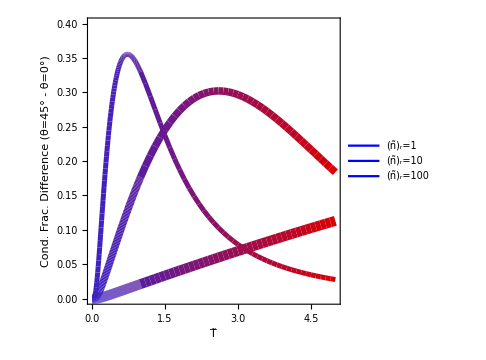

```mathematica
(*Figure-2 d data Plotting*)

heatcolors1 =Table[Blend[{RGBColor["#122DF7"], RGBColor["#DC0000"]}, i/Length[T̃]], {i, 1, Length[T̃]}];


CreateGradientLines[data_List,colorGradient_List,thickness_]:=Module[{min,max,linesWithColors},min=Min[data[[All,1]]];
max=Max[data[[All,1]]];
linesWithColors=Table[{Thickness[thickness],Blend[colorGradient,(data[[i,1]]-min)/(max-min)],Line[{data[[i]],data[[i+1]]}]},{i,1,Length[data]-1}];
Flatten[linesWithColors,1]];

gradientPlots=Table[If[i==1,CreateGradientLines[plot2[[i]],heatcolors1,0.005+0.005*i],If[i==2,CreateGradientLines[plot2[[i]],heatcolors1,0.005+0.005*i],If[i==3,CreateGradientLines[plot2[[i]],heatcolors1,0.005+0.005*i],{}]]],{i,Length[plot2]}];


figure2d=Graphics[{CapForm["Round"],Join@@gradientPlots},

Frame->True,
FrameLabel->{Style["T̃",Black,25],Style["Cond. Frac. Difference\n(θ=45° - θ=0°)",Black,25,Italic]},
FrameTicksStyle->Directive[Black,25,Thickness[0.005]],PlotRange->{0,0.4},
ImageSize->Medium,
AspectRatio->1
];

Export["C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\Figures\\Figure2\\figure2_d.pdf",figure2d=Legended[ figure2d,
LineLegend[{Blue,Blue,Blue},{"(ñ)_r="<>ToString[OverTilde[nr][[1]]],"(ñ)_r="<>ToString[OverTilde[nr][[2]]],"(ñ)_r="<>ToString[OverTilde[nr][[3]]]},LabelStyle->{FontSize->20}]]
]
Print[figure2d]
```

### Figure-3 a data creation

```mathematica
Lt= 100*10^-9;
OverTilde[nr]={ 1};
thmin=1;thmax=46;thstep = 1;
T̃ = { 0.1 , 0.5, 1 ,2};
CvplotList1 ={};



fun1[th_,dimlessT_,nr_] :=
SumCvBE[eigenvalues[[th]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[th]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]]

For[i=1,i<=Length[OverTilde[nr]],i++,
Cvplot ={
Table[{th-1,fun1[th,T̃[[1]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun1[th,T̃[[2]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun1[th,T̃[[3]],  OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}],
Table[{th-1,fun1[th,T̃[[4]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}]};
AppendTo[CvplotList1,Cvplot];
];
```

General::munfl: 1/(4.98979×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.00409×10^-308+1.308082992754×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.01717×10^-308+1.291916690899×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Figure-3 a data save

```mathematica
For[i=1,i<=Length[OverTilde[nr]],i++,
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure3_a"<>ToString[OverTilde[nr][[i]]]<>".csv",CvplotList1[[i]],"CSV"];
];
```

### Figure-3 b data creation

```mathematica
Tmin=1;Tmax=4;Tstep = 0.1;
Tmin2=0.03;Tmax2=1;Tstep2 = 0.01;
th = { 0 ,5, 10, 20 ,30,45};
CvplotList2 ={};

fun2[th_,dimlessT_,nr_] :=
SumCvBE[eigenvalues[[th+1]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[th+1]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]]

For[i=1,i<=Length[OverTilde[nr] ],i++,
Cvplot={Join[Table[{Tt,fun2[th[[1]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun2[th[[1]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun2[th[[2]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun2[th[[2]],Tt,OverTilde[nr][[i]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun2[th[[3]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun2[th[[3]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun2[th[[4]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun2[th[[4]],Tt,OverTilde[nr][[i]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun2[th[[5]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun2[th[[5]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin,Tmax,Tstep}]],
Join[Table[{Tt,fun2[th[[6]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin2,Tmax2,Tstep2}],
Table[{Tt,fun2[th[[6]],Tt ,OverTilde[nr][[i]]]},{Tt,Tmin,Tmax,Tstep}]]};
AppendTo[CvplotList2,Cvplot];
];
```

General::munfl: 1/(7.53323×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(1.152×10^308) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.68054×10^-309+1.688026175784×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Figure-3 b data save

```mathematica
For[i=1,i<=Length[OverTilde[nr] ],i++,
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure3_b_nr"<>ToString[OverTilde[nr][[i]]]<>".csv",CvplotList2[[i]],"CSV"];
];
```

### Figure-3 a,b data Plotting

```mathematica
CvplotList = {};
shapecolors1 =   {RGBColor["#eb5e28"], RGBColor["#f9a03f"],RGBColor["#f3c053"],RGBColor["#a1c349"],RGBColor["#87a330"],RGBColor["#6a8532"]};
shapecolors2 =Table[Blend[{RGBColor["#FFD940"], RGBColor["#003403"]}, i/Length[T̃]], {i, 1, Length[T̃]}];

color=heatcolors2;
styles=Map[Directive[#,Thickness[0.015]]&,color];
Cvplotdata1 = ListLinePlot[CvplotList1,
Frame-> True,
AspectRatio->1,
PlotRange -> {0,1.2},
ImageSize->Medium,
PlotStyle->styles
];
AppendTo[CvplotList,Cvplotdata1];


color=shapecolors1;
styles=Map[Directive[#,Thickness[0.015]]&,color];
Cvplotdata2 = ListLinePlot[CvplotList2,
Frame-> True,
AspectRatio->1,
PlotRange -> {0,1.2},
ImageSize->Medium,
PlotStyle->styles
];
AppendTo[CvplotList,Cvplotdata2];



Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\Figures\\Figure3\\figure3_ab.pdf",CvplotList=Legended[ResourceFunction["PlotGrid"][{CvplotList},
FrameTicksStyle->Directive[Black,15,Thick],FrameLabel->{None,Style["Specific Heat [k_B]",Black,Italic,15]}],
LineLegend[shapecolors1,Table["θ="<>ToString[th[[i]]]<>"°",{i,1,Length[th]}],LabelStyle->{FontSize->15}]]
]
Print[CvplotList]
```

C:\Users\Cem\Desktop\Bose-einstein_Condensation\ShapeEffects\Final\Figures\Figure3\figure3_ab.pdf

-Graphics-

### Figure-4 data creation and save to files

```mathematica
Lt= 100*10^-9;
OverTilde[nr]=10;
thmin=1;thmax=46;thstep = 1;
T̃ =  10 ;


fb0=Table[{x,BoseFac[eigenvalues[[1]][[x]],calcT[T̃ ],Lt,Summucalc[eigenvalues[[1]],calcT[T̃ ],Lt, calcN[calcT[T̃ ],Lt,OverTilde[nr]]]]},{x,1,200}];
fb5=Table[{x,BoseFac[eigenvalues[[6]][[x]],calcT[T̃ ],Lt,Summucalc[eigenvalues[[6]],calcT[T̃ ],Lt, calcN[calcT[T̃ ],Lt,OverTilde[nr]]]]},{x,1,200}];
fb45=Table[{x,BoseFac[eigenvalues[[46]][[x]],calcT[T̃ ],Lt,Summucalc[eigenvalues[[46]],calcT[T̃ ],Lt, calcN[calcT[T̃ ],Lt,OverTilde[nr]]]]},{x,1,200}];
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure4_0degree_EivsfB_T10_nr10.csv",fb0,"CSV"];
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure4_5degree_EivsfB_T10_nr10.csv",fb5,"CSV"];
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure4_45degree_EivsfB_T10_nr10.csv",fb45,"CSV"];
```

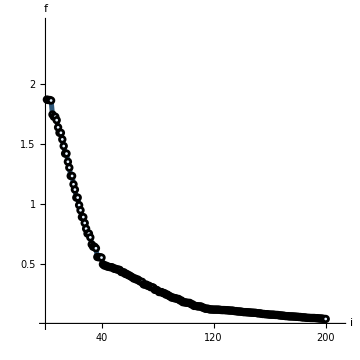
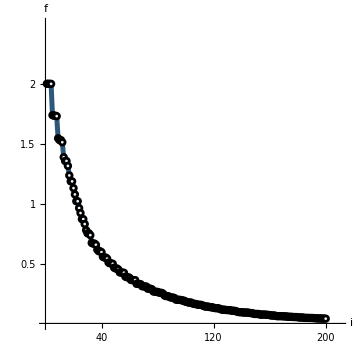
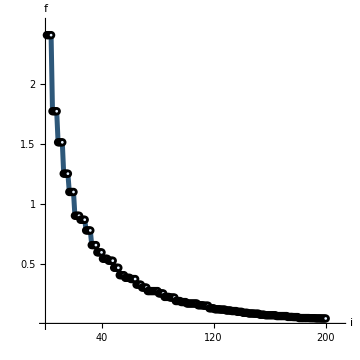

```mathematica
(*Fıgure-4 data Plotting and save to files*)
plotList = {fb0 ,fb5 , fb45};
Row[Table[
ListPlot[plotList[[i]],Joined->True,PlotMarkers->{Graphics[{RGBColor["#e5f2ff"],EdgeForm[{Black,Thickness[0.1]}],Disk[]}],0.025},
PlotRange->{{0,210},{0,2.5}}, 
PlotStyle->{RGBColor["#2e587a"],Thickness[0.01]},
AxesLabel->{Style["i",Italic,Black,30],Style["f",Italic,Black,30]},
LabelStyle->Directive[Black,FontSize->30],
AxesStyle->Directive[Black,Thickness[0.01]],
Ticks->{ {40,120,200},{0.5,1,1.5,2}},
TicksStyle->Directive[Black, Thickness[0.01]],
ImageSize->Medium,
AspectRatio->1] ,{i,1,Length[plotList]}]  ]
```

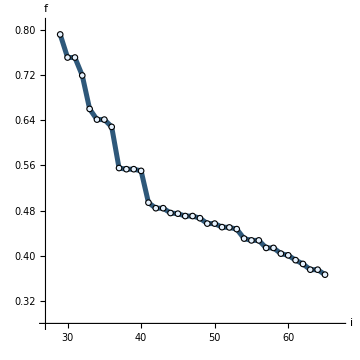
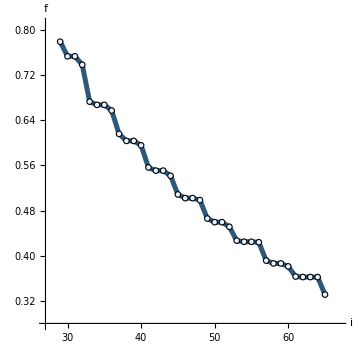
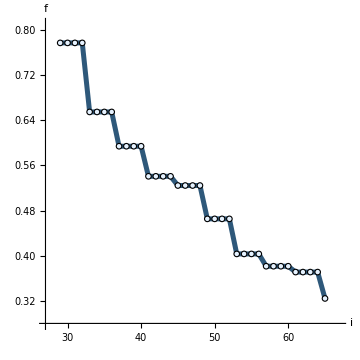

```mathematica
plotList = {fb0 ,fb5 , fb45};
Row[Table[
ListPlot[plotList[[i]][[29;;65]],Joined->True,PlotMarkers->{Graphics[{RGBColor["#e5f2ff"],EdgeForm[Black],Disk[]}],0.05},
PlotRange->{{27,67}, {0.28,0.81}}, 
PlotStyle->{RGBColor["#2e587a"],Thickness[0.01]},
AxesLabel->{Style["i",Italic,Black,25],Style["f",Italic,Black,25]},
LabelStyle->Directive[Black,FontSize->25,"Sa"],
TicksStyle->Directive[Black],
ImageSize->Medium,
AspectRatio->1] ,{i,1,Length[plotList]}]  ]
```

## Other Supplementary Calculations

### Chemical Energy, Free Energy, and Entropy for figure a,b,c

```mathematica
Lt= 100*10^-9;
OverTilde[nr]={ 1, 10 , 100};
thmin=1;thmax=46;thstep = 1;
T̃ = { 0.1 , 0.5, 1 ,2,5};
figure2mu ={};
figure2S={};
figure2F ={};

fun1[th_,dimlessT_,nr_] :=
Summucalc[eigenvalues[[th]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]
fun2[th_,dimlessT_,nr_] :=
SumSBE[eigenvalues[[th]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[th]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]]
fun3[th_,dimlessT_,nr_] :=
SumFBE[eigenvalues[[th]],calcT[dimlessT],Lt,Summucalc[eigenvalues[[th]],calcT[dimlessT],Lt, calcN[calcT[dimlessT],Lt,nr]]]


Quiet[ For[i=1,i<=Length[OverTilde[nr]],i++,
mu={For[j=1,j<=3,j++,
Table[{th-1,fun1[th,T̃[[1]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}]];};
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure2_mu_nr"<>ToString[OverTilde[nr][[i]]]<>".csv",mu,"CSV"];
AppendTo[figure2mu,mu];
];];
Quiet[ For[i=1,i<=Length[OverTilde[nr]],i++,
S={For[j=1,j<=3,j++,
Table[{th-1,fun1[th,T̃[[1]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}]];};
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure2_S_nr"<>ToString[OverTilde[nr][[i]]]<>".csv",S,"CSV"];
AppendTo[figure2S,S];
];];Quiet[ For[i=1,i<=Length[OverTilde[nr]],i++,
F={For[j=1,j<=3,j++,
Table[{th-1,fun1[th,T̃[[1]], OverTilde[nr][[i]]]} ,{th,thmin,thmax,thstep}]];};
Export[ "C:\\Users\\Cem\\Desktop\\Bose-einstein_Condensation\\ShapeEffects\\Final\\datasets\\figure2_F_nr"<>ToString[OverTilde[nr][[i]]]<>".csv",F,"CSV"];
AppendTo[figure2F,F];
];];
```

General::munfl: 1/(4.49605×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.67386×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.44957×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.401347

```mathematica
plotListmu= {};
plotListS= {};
plotListF= {};
heatcolors = Table[Blend[{RGBColor["#122DF7"], RGBColor["#DC0000"]}, i/Length[T̃]], {i, 1, Length[T̃]}];

For[i=1,i<=Length[OverTilde[nr]],i++,
thicks=0.005 + 0.005 *i;
color=ToExpression["heatcolors"];
styles=Map[Directive[#,Thickness[thicks]]&,color];
plotsmu= ListLinePlot[figure2abc[[i]],
PlotStyle->styles,
Frame-> True,
AspectRatio->1,
PlotRange -> {0,1.1}
];
plotsS= ListLinePlot[figure2abc[[i]],
PlotStyle->styles,
Frame-> True,
AspectRatio->1,
PlotRange -> {0,1.1}
];
plotsF= ListLinePlot[figure2abc[[i]],
PlotStyle->styles,
Frame-> True,
AspectRatio->1,
PlotRange -> {0,1.1}
];
AppendTo[plotListmu,plotsmu];
AppendTo[plotListS,plotsS];
AppendTo[plotListF,plotsF];
];

modifiedPlotListmu=plotListmu/. {Graphics[content_,options___]:>Graphics[content,options,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[Black,15,Thickness[0.005]]]};
modifiedPlotListS=plotListS/. {Graphics[content_,options___]:>Graphics[content,options,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[Black,15,Thickness[0.005]]]};

modifiedPlotListF=plotListF/. {Graphics[content_,options___]:>Graphics[content,options,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[Black,15,Thickness[0.005]]]};


muplotfinal=Legended[ResourceFunction["PlotGrid"][{modifiedPlotListmu},
ImageSize->Large,
FrameLabel->{Style["θ",Black,Italic,15],Style["λ",Black,Italic,15]}],LineLegend[ heatcolors,Table["T̃="<>ToString[T̃[[i]]],{i,1, Length[T̃]}],
LabelStyle->{FontSize->12}]
]
Splotfinal=Legended[ResourceFunction["PlotGrid"][{modifiedPlotListS},
ImageSize->Large,
FrameLabel->{Style["θ",Black,Italic,15],Style["S/NK_B",Black,Italic,15]}],LineLegend[ heatcolors,Table["T̃="<>ToString[T̃[[i]]],{i,1, Length[T̃]}],
LabelStyle->{FontSize->12}]
]
Fplotfinal=Legended[ResourceFunction["PlotGrid"][{modifiedPlotListF},
ImageSize->Large,
FrameLabel->{Style["θ",Black,Italic,15],Style["F/NK_BT",Black,Italic,15]}],LineLegend[ heatcolors,Table["T̃="<>ToString[T̃[[i]]],{i,1, Length[T̃]}],
LabelStyle->{FontSize->12}]
]
Print[muplotfinal]
{{Print[Splotfinal]}, {Print[Fplotfinal]}}
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

{{Null},{Null}}

```mathematica
plotListmu
```